# Calculate the inertia of the coffee table

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/nathan/olin/fall2016/QEA-BB8/inertiaCalculations

```mathematica
data=Import["coffeeTableInertia.csv","Data"]
```

{{time,x,y,z},{0.004,0.18,0.81,0.02},{0.005,0.16,0.55,0.02},2660,{11.776,0.01,0.32,-0.08},{11.777,0.05,0.33,-0.06},{11.777,0.06,0.26,-0.07}}
 |  |  |  |

```mathematica
start=1150;
end=2050;
t=Transpose[data][[1]][[start;;end]];
x=Transpose[data][[2]][[start;;end]];
y=Transpose[data][[3]][[start;;end]];
z=Transpose[data][[4]][[start;;end]];
```

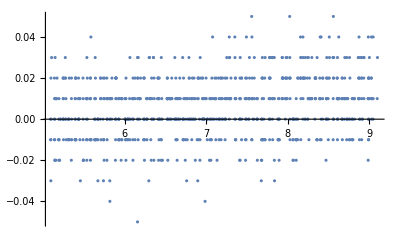

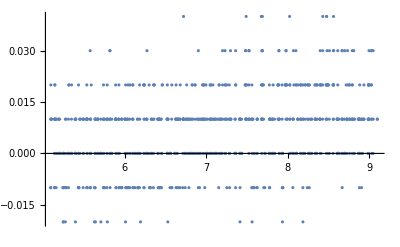

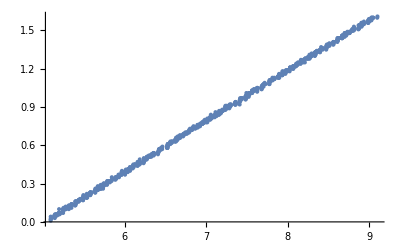

```mathematica
ListPlot[Transpose@{t,x}]
ListPlot[Transpose@{t,y}]
ListPlot[Transpose@{t,z}]
```

```mathematica
Fit[Transpose@{t,z},{1,a},a]
```

-1.99333+0.397531 a

```mathematica
α=0.3975306487372306
```

0.397531

```mathematica
r=.445/2
```

0.2225

```mathematica
f=9.8*.500
```

4.9

```mathematica
t=r*f
```

1.09025

```mathematica
i=t/α
```

2.74256

```mathematica
30*((.75)/2)^2
```

4.21875